```mathematica
(* The cases in this notebook all have lam > 0. *)
```

6.08623

7.6189

0.+0. ⅈ

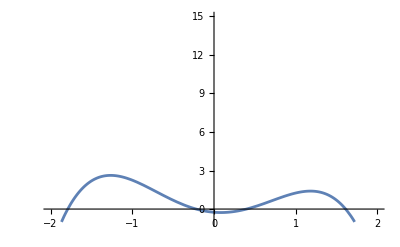

{{a→-1.78923},{a→-0.218388},{a→0.397315},{a→1.61031}}

{1.61031+0. ⅈ,0.397315+0. ⅈ,-0.218388+0. ⅈ,-1.78923+0. ⅈ}

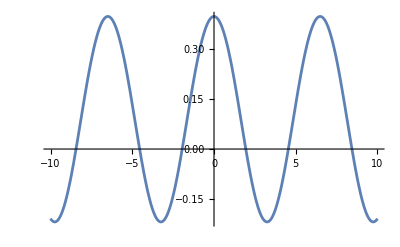

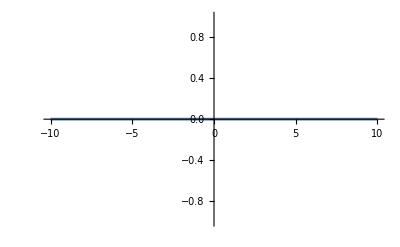

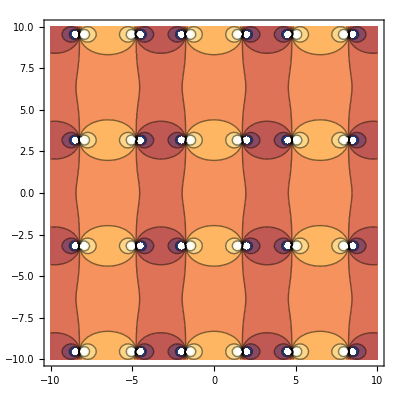

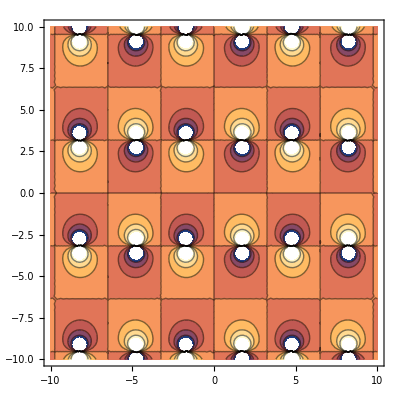

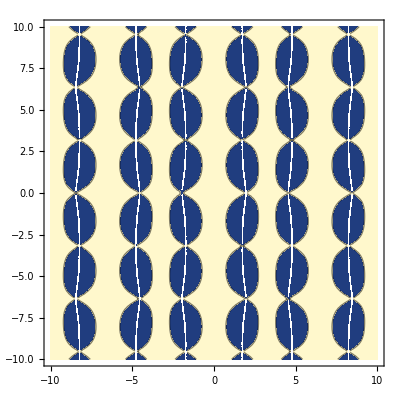

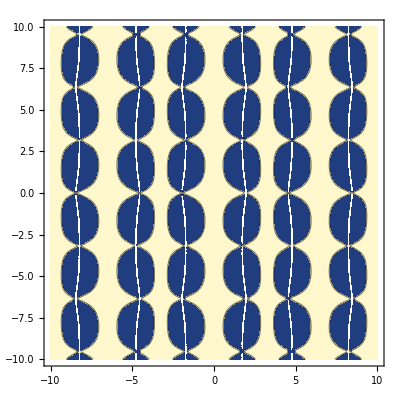

-1.+0. ⅈ

0.-10.8828 ⅈ

6.4946+0. ⅈ

0.-6.35671 ⅈ

0.600886+0. ⅈ

3.07094×10^-16-5.65479 ⅈ

-Graphics-

-Graphics-

0.-0.14467 ⅈ

0.614738+6.71398×10^-30 ⅈ

0.614738+0. ⅈ

```mathematica
(* Closed, kappa > 0, 4 real roots: 2 kt^3/mt^2 > gp(x) > gm(x) *)
(* In this case, there is a contour satisfying Witten's criterion. *)

Clear[lam,k,m,r,kt,mt,rt,f,Pp,Qq,xh,z0,e0,app,apm,amp,amm]

lam=1.;
k=1.;
m=.5;
x=1;
r=(x m^2)/k;
gp[x]=((1+8 x)+(1+8/3 x)√(1+32/3 x))/(1+3 √(1+32/3 x));
gm[x]=((1+8 x)-(1+8/3 x)√(1+32/3 x))/(1-3 √(1+32/3 x));
kt=k/lam;
mt=m/lam;
rt=r/lam;
(2 kt^3)/mt^2-gp[x]
(2 kt^3)/mt^2-gm[x]
f=a^4-3 kt a^2+mt a+rt;
V=-lam f;
Pp=-4/3 rt-kt^2;
Qq=-mt^2/2+kt^3-4 kt rt;
xh=(-Qq+√(Qq^2+Pp^3))^(1/3);
z0=2 kt+xh-Pp/xh;
e0=z0^(1/2);
app=1/2((+e0)+√(-(+e0)^2-2mt/(+e0)+6 kt));
apm=1/2((+e0)-√(-(+e0)^2-2mt/(+e0)+6 kt));
amp=1/2((-e0)+√(-(-e0)^2-2mt/(-e0)+6 kt));
amm=1/2((-e0)-√(-(-e0)^2-2mt/(-e0)+6 kt));
app+apm+amp+amm

Plot[V,{a,-2,2},PlotRange->{{-2,2},{-1,15}}]
Solve[V==0,a]
{app,apm,amp,amm}

a1=app;
a2=apm;
a3=amp;
a4=amm;

mm=((a2-a3)(a1-a4))/((a1-a3)(a2-a4));
rho=1/2 √(lam/3(a1-a3)(a2-a4));
a[tau_]:=(a2(a3-a1)-a1(a3-a2)JacobiSN[rho tau,mm]^2)/((a3-a1)-(a3-a2)JacobiSN[rho tau,mm]^2)
Plot[Re[a[tau]],{tau,-10,10}]
Plot[Im[a[tau]],{tau,-10,10}]
ContourPlot[Re[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[π-3Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]
ContourPlot[π-4Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]
taustar=1/rho InverseJacobiSN[√((a2-a4)/(a1-a4)),mm];
(a2-a1)/(√((a1-a3)(a1-a4))JacobiCN[rho taustar,mm]JacobiDN[rho taustar,mm])
-2 π ⅈ √(3/lam)

2 EllipticK[mm]/rho
-2ⅈ EllipticK[1-mm]/rho

NIntegrate[a[tau],{tau,0,2 EllipticK[mm]/rho}]
NIntegrate[a[tau],{tau,0,-2ⅈ EllipticK[1-mm]/rho}]

SdS=(24 π^2)/lam;

Sintegrand[tau_]:=-(2 π^2)/lam^(3/2)6 ⅈ (a'[tau])^2
ContourPlot[Re[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]

1/SdS NIntegrate[Sintegrand[tau],{tau,0,2 EllipticK[mm]/rho}]
1/SdS NIntegrate[Sintegrand[tau],{tau,0,-2ⅈ EllipticK[1-mm]/rho}]

a12=a1-a2;
a13=a1-a3;
a14=a1-a4;
a23=a2-a3;
a24=a2-a4;
a34=a3-a4;
m0=(a12 a34)/(a13 a24);
CK=a13(a34^2-a12^2-4/3 a14 a24);
CE=(8 k)/lam*(a13 a24)/a23;
CPi=(a13^2-a24^2)(a14-a23);
Sanalytic=1/SdS 2 π^2(√3)/(2 lam)*a23/(√(a13 a24))(CK*EllipticK[m0]+CE EllipticE[m0]+CPi EllipticPi[a12/a13,m0])
```

-1.02488

0.507785

0.+0. ⅈ

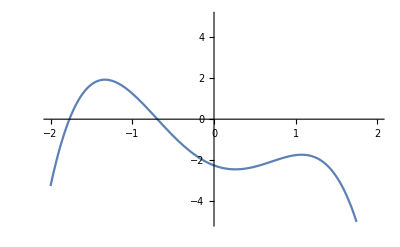

{{a→-1.76887},{a→-0.693091},{a→1.23098-0.565638 ⅈ},{a→1.23098+0.565638 ⅈ}}

{1.23098+0.565638 ⅈ,1.23098-0.565638 ⅈ,-0.693091,-1.76887}

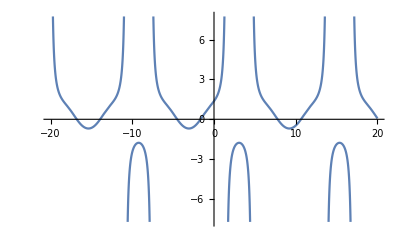

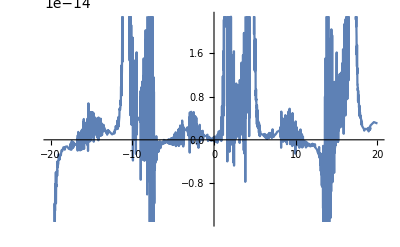

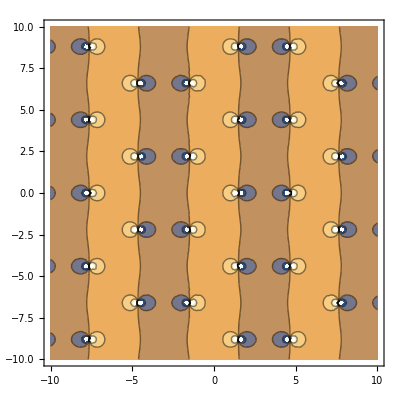

-Graphics-

-Graphics-

-Graphics-

-1.+5.88834×10^-16 ⅈ

0.+10.8828 ⅈ

6.1447-2.20053 ⅈ

-2.77556×10^-17+4.40105 ⅈ

0.205506-2.8565 ⅈ

-3.33067×10^-16+5.713 ⅈ

-Graphics-

-Graphics-

-0.348669-1.4299 ⅈ

0.697337-7.64926×10^-16 ⅈ

-0.697337+1.63452×10^-15 ⅈ

```mathematica
(* Closed, kappa > 0, 2 real roots: gp(x) > 2 kt^3/mt^2 > gm(x) *)

Clear[lam,k,m,r,kt,mt,rt,f,Pp,Qq,xh,z0,e0,app,apm,amp,amm]

lam=1.;
k=1.;
m=1.5;
x=1;
r=(x m^2)/k;
gp[x]=((1+8 x)+(1+8/3 x)√(1+32/3 x))/(1+3 √(1+32/3 x));
gm[x]=((1+8 x)-(1+8/3 x)√(1+32/3 x))/(1-3 √(1+32/3 x));
kt=k/lam;
mt=m/lam;
rt=r/lam;
(2 kt^3)/mt^2-gp[x]
(2 kt^3)/mt^2-gm[x]
f=a^4-3 kt a^2+mt a+rt;
V=-lam f;
Pp=-4/3 rt-kt^2;
Qq=-mt^2/2+kt^3-4 kt rt;
xh=(-Qq+√(Qq^2+Pp^3))^(1/3);
z0=2 kt+xh-Pp/xh;
e0=z0^(1/2);
app=1/2((+e0)+√(-(+e0)^2-2mt/(+e0)+6 kt));
apm=1/2((+e0)-√(-(+e0)^2-2mt/(+e0)+6 kt));
amp=1/2((-e0)+√(-(-e0)^2-2mt/(-e0)+6 kt));
amm=1/2((-e0)-√(-(-e0)^2-2mt/(-e0)+6 kt));
app+apm+amp+amm

Plot[V,{a,-2,2},PlotRange->{{-2,2},{-5,5}}]
Solve[V==0,a]
{app,apm,amp,amm}

a1=app;
a2=apm;
a3=amp;
a4=amm;

mm=((a2-a3)(a1-a4))/((a1-a3)(a2-a4));
rho=1/2 √(lam/3(a1-a3)(a2-a4));
a[tau_]:=(a2(a3-a1)-a1(a3-a2)JacobiSN[rho tau+ⅈ/2 EllipticK[1-mm],mm]^2)/((a3-a1)-(a3-a2)JacobiSN[rho tau+ⅈ/2 EllipticK[1-mm],mm]^2)
Plot[Re[a[tau]],{tau,-20,20}]
Plot[Im[a[tau]],{tau,-20,20}]
ContourPlot[Re[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[π-3Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]
ContourPlot[π-4Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]

taustar=1/rho InverseJacobiSN[√((a2-a4)/(a1-a4)),mm];
(a2-a1)/(√((a1-a3)(a1-a4))JacobiCN[rho taustar,mm]JacobiDN[rho taustar,mm])
2 π ⅈ √(3/lam)

2 EllipticK[mm]/rho
2 ⅈ EllipticK[1-mm]/rho

NIntegrate[a[tau],{tau,0,2 EllipticK[mm]/rho}]
NIntegrate[a[tau],{tau,0,2 ⅈ EllipticK[1-mm]/rho}]

SdS=(24 π^2)/lam;

Sintegrand[tau_]:=-(2 π^2)/lam^(3/2)6 ⅈ (a'[tau])^2
ContourPlot[Re[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]

1/SdS NIntegrate[Sintegrand[tau],{tau,0,2 EllipticK[mm]/rho}]
1/SdS NIntegrate[Sintegrand[tau],{tau,0,2ⅈ EllipticK[1-mm]/rho}]

a12=a1-a2;
a13=a1-a3;
a14=a1-a4;
a23=a2-a3;
a24=a2-a4;
a34=a3-a4;
m0=(a12 a34)/(a13 a24);
CK=a13(a34^2-a12^2-4/3 a14 a24);
CE=(8 k)/lam*(a13 a24)/a23;
CPi=(a13^2-a24^2)(a14-a23);
Sanalytic=1/SdS 2 π^2(√3)/(2 lam)*a23/(√(a13 a24))(CK*EllipticK[m0]+CE EllipticE[m0]+CPi EllipticPi[a12/a13,m0])
```

```mathematica
(* Closed, kappa > 0, 0 real roots: gp(x) > gm(x) > 2 kt^3/mt^2 *)

Clear[lam,k,m,r,kt,mt,rt,f,Pp,Qq,xh,z0,e0,app,apm,amp,amm]

lam=1.;
k=1.;
m=3;
x=1;
r=(x m^2)/k;
gp[x]=((1+8 x)+(1+8/3 x)√(1+32/3 x))/(1+3 √(1+32/3 x));
gm[x]=((1+8 x)-(1+8/3 x)√(1+32/3 x))/(1-3 √(1+32/3 x));
kt=k/lam;
mt=m/lam;
rt=r/lam;
(2 kt^3)/mt^2-gp[x]
(2 kt^3)/mt^2-gm[x]
f=a^4-3 kt a^2+mt a+rt;
V=-lam f;
Pp=-4/3 rt-kt^2;
Qq=-mt^2/2+kt^3-4 kt rt;
xh=(-Qq+√(Qq^2+Pp^3))^(1/3);
z0=2 kt+xh-Pp/xh;
e0=z0^(1/2);
app=1/2((+e0)+√(-(+e0)^2-2mt/(+e0)+6 kt));
apm=1/2((+e0)-√(-(+e0)^2-2mt/(+e0)+6 kt));
amp=1/2((-e0)+√(-(-e0)^2-2mt/(-e0)+6 kt));
amm=1/2((-e0)-√(-(-e0)^2-2mt/(-e0)+6 kt));
app+apm+amp+amm

Plot[V,{a,-2,2},PlotRange->{{-2,2},{-12,1}}]
Solve[V==0,a]
{app,apm,amp,amm}

a1=app;
a2=apm;
a3=amp;
a4=amm;

mm=((a2-a3)(a1-a4))/((a1-a3)(a2-a4));
rho=1/2 √(lam/3(a1-a3)(a2-a4));
a[tau_]:=(a2(a3-a1)-a1(a3-a2)JacobiSN[rho tau+ⅈ/2 EllipticK[1-mm],mm]^2)/((a3-a1)-(a3-a2)JacobiSN[rho tau+ⅈ/2 EllipticK[1-mm],mm]^2)
Plot[Re[a[tau]],{tau,-10,10}]
Plot[Im[a[tau]],{tau,-10,10}]
ContourPlot[Re[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[π-3Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]
ContourPlot[π-4Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]

taustar=1/rho InverseJacobiSN[√((a2-a4)/(a1-a4)),mm];
(a2-a1)/(√((a1-a3)(a1-a4))JacobiCN[rho taustar,mm]JacobiDN[rho taustar,mm])
2 π ⅈ √(3/lam)

2 EllipticK[mm]/rho
2 ⅈ EllipticK[1-mm]/rho

NIntegrate[a[tau],{tau,0,2 EllipticK[mm]/rho}]
NIntegrate[a[tau],{tau,0,2 ⅈ EllipticK[1-mm]/rho}]

SdS=(24 π^2)/lam;

Sintegrand[tau_]:=-(2 π^2)/lam^(3/2)6 ⅈ (a'[tau])^2
ContourPlot[Re[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]

1/SdS NIntegrate[Sintegrand[tau],{tau,0,2 EllipticK[mm]/rho}]
1/SdS NIntegrate[Sintegrand[tau],{tau,0,2ⅈ EllipticK[1-mm]/rho}]

a12=a1-a2;
a13=a1-a3;
a14=a1-a4;
a23=a2-a3;
a24=a2-a4;
a34=a3-a4;
m0=(a12 a34)/(a13 a24);
CK=a13(a34^2-a12^2-4/3 a14 a24);
CE=(8 k)/lam*(a13 a24)/a23;
CPi=(a13^2-a24^2)(a14-a23);
Sanalytic=1/SdS 2 π^2(√3)/(2 lam)*a23/(√(a13 a24))(CK*EllipticK[m0]+CE EllipticE[m0]+CPi EllipticPi[a12/a13,m0])
```

-1.69155

-0.158882

0.+0. ⅈ

-Graphics-

{{a→-1.50682-0.522272 ⅈ},{a→-1.50682+0.522272 ⅈ},{a→1.50682-1.12616 ⅈ},{a→1.50682+1.12616 ⅈ}}

{1.50682+1.12616 ⅈ,1.50682-1.12616 ⅈ,-1.50682+0.522272 ⅈ,-1.50682-0.522272 ⅈ}

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

-1.-1.2816×10^-15 ⅈ

0.+10.8828 ⅈ

4.55544-3.34673 ⅈ

-5.89986×10^-17+3.34673 ⅈ

-1.05505-0.265982 ⅈ

4.44089×10^-16+5.70738 ⅈ

-Graphics-

-Graphics-

-2.15588-4.45764 ⅈ

3.51623+0. ⅈ

-3.51623-3.33314×10^-15 ⅈ

```mathematica
(* Open, kappa < 0, 2 real roots: gm(x) > 2 kt^3/mt^2 *)

Clear[lam,k,m,r,kt,mt,rt,f,Pp,Qq,xh,z0,e0,app,apm,amp,amm]

lam=1.;
k=-1.;
m=2;
x=-0.05;
r=(x m^2)/k;
gp[x]=((1+8 x)+(1+8/3 x)√(1+32/3 x))/(1+3 √(1+32/3 x));
gm[x]=((1+8 x)-(1+8/3 x)√(1+32/3 x))/(1-3 √(1+32/3 x));
kt=k/lam;
mt=m/lam;
rt=r/lam;
(2 kt^3)/mt^2-gm[x]
f=a^4-3 kt a^2+mt a+rt;
V=-lam f;
Pp=-4/3 rt-kt^2;
Qq=-mt^2/2+kt^3-4 kt rt;
xh=(-Qq+√(Qq^2+Pp^3))^(1/3);
z0=2 kt+xh-Pp/xh;
e0=z0^(1/2);
app=1/2((+e0)+√(-(+e0)^2-2mt/(+e0)+6 kt));
apm=1/2((+e0)-√(-(+e0)^2-2mt/(+e0)+6 kt));
amp=1/2((-e0)+√(-(-e0)^2-2mt/(-e0)+6 kt));
amm=1/2((-e0)-√(-(-e0)^2-2mt/(-e0)+6 kt));
app+apm+amp+amm

Plot[V,{a,-2,2},PlotRange->{{-1,1},{-1,1}}]
Solve[V==0,a]
{app,apm,amp,amm}

a1=app;
a2=apm;
a3=amp;
a4=amm;

mm=((a2-a3)(a1-a4))/((a1-a3)(a2-a4));
rho=1/2 √(lam/3(a1-a3)(a2-a4));
a[tau_]:=(a2(a3-a1)-a1(a3-a2)JacobiSN[rho tau+ⅈ/2 EllipticK[1-mm],mm]^2)/((a3-a1)-(a3-a2)JacobiSN[rho tau+ⅈ/2 EllipticK[1-mm],mm]^2)
Plot[Re[a[tau]],{tau,-10,10}]
Plot[Im[a[tau]],{tau,-10,10}]
ContourPlot[Re[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[π-3Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]
ContourPlot[π-4Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]

taustar=1/rho InverseJacobiSN[√((a2-a4)/(a1-a4)),mm];
(a2-a1)/(√((a1-a3)(a1-a4))JacobiCN[rho taustar,mm]JacobiDN[rho taustar,mm])
2 π ⅈ √(3/lam)

2 EllipticK[mm]/rho
2ⅈ EllipticK[1-mm]/rho

NIntegrate[a[tau],{tau,0,2 EllipticK[mm]/rho}]
NIntegrate[a[tau],{tau,0,2ⅈ EllipticK[1-mm]/rho}]

SdS=(24 π^2)/lam;
Sintegrand[tau_]:=-(2 π^2)/lam^(3/2)6 ⅈ (a'[tau])^2
ContourPlot[Re[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]

1/SdS NIntegrate[Sintegrand[tau],{tau,0,2 EllipticK[mm]/rho}]
1/SdS NIntegrate[Sintegrand[tau],{tau,0,2ⅈ EllipticK[1-mm]/rho}]

a12=a1-a2;
a13=a1-a3;
a14=a1-a4;
a23=a2-a3;
a24=a2-a4;
a34=a3-a4;
m0=(a12 a34)/(a13 a24);
CK=a13(a34^2-a12^2-4/3 a14 a24);
CE=(8 k)/lam*(a13 a24)/a23;
CPi=(a13^2-a24^2)(a14-a23);
Sanalytic=1/SdS 2 π^2(√3)/(2 lam)*a23/(√(a13 a24))(CK*EllipticK[m0]+CE EllipticE[m0]+CPi EllipticPi[a12/a13,m0])
```

-0.49242

0.+0. ⅈ

-Graphics-

{{a→-0.491448},{a→-0.122694},{a→0.307071-1.79515 ⅈ},{a→0.307071+1.79515 ⅈ}}

{0.307071+1.79515 ⅈ,0.307071-1.79515 ⅈ,-0.122694,-0.491448}

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

-1.-4.63842×10^-17 ⅈ

0.+10.8828 ⅈ

6.87938-2.86333 ⅈ

-1.11022×10^-16+5.72666 ⅈ

-0.93741-4.5704 ⅈ

-2.22045×10^-15+9.14079 ⅈ

-Graphics-

-Graphics-

-0.877622+0.974984 ⅈ

1.75524+8.83115×10^-14 ⅈ

-1.75524+8.65333×10^-16 ⅈ

```mathematica
(* Open, kappa < 0, 0 real roots: 2 kt^3/mt^2 > gm(x) *)

Clear[lam,k,m,r,kt,mt,rt,f,Pp,Qq,xh,z0,e0,app,apm,amp,amm]

lam=1.;
k=-1.;
m=2;
x=-1;
r=(x m^2)/k;
gp[x]=((1+8 x)+(1+8/3 x)√(1+32/3 x))/(1+3 √(1+32/3 x));
gm[x]=((1+8 x)-(1+8/3 x)√(1+32/3 x))/(1-3 √(1+32/3 x));
kt=k/lam;
mt=m/lam;
rt=r/lam;
(2 kt^3)/mt^2-gm[x]
f=a^4-3 kt a^2+mt a+rt;
V=-lam f;
Pp=-4/3 rt-kt^2;
Qq=-mt^2/2+kt^3-4 kt rt;
xh=(-Qq+√(Qq^2+Pp^3))^(1/3);
z0=2 kt+xh-Pp/xh;
e0=z0^(1/2);
app=1/2((+e0)+√(-(+e0)^2-2mt/(+e0)+6 kt));
apm=1/2((+e0)-√(-(+e0)^2-2mt/(+e0)+6 kt));
amp=1/2((-e0)+√(-(-e0)^2-2mt/(-e0)+6 kt));
amm=1/2((-e0)-√(-(-e0)^2-2mt/(-e0)+6 kt));
app+apm+amp+amm

Plot[V,{a,-2,2},PlotRange->{{-2,2},{-10,5}}]
Solve[V==0,a]
{app,apm,amp,amm}

a1=app;
a2=apm;
a3=amp;
a4=amm;

mm=((a2-a3)(a1-a4))/((a1-a3)(a2-a4));
rho=1/2 √(lam/3(a1-a3)(a2-a4));
a[tau_]:=(a2(a3-a1)-a1(a3-a2)JacobiSN[rho tau+ⅈ/2 EllipticK[1-mm],mm]^2)/((a3-a1)-(a3-a2)JacobiSN[rho tau+ⅈ/2 EllipticK[1-mm],mm]^2)
Plot[Re[a[tau]],{tau,-10,10}]
Plot[Im[a[tau]],{tau,-10,10}]
ContourPlot[Re[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[π-3Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]
ContourPlot[π-4Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]

taustar=1/rho InverseJacobiSN[√((a2-a4)/(a1-a4)),mm];
(a2-a1)/(√((a1-a3)(a1-a4))JacobiCN[rho taustar,mm]JacobiDN[rho taustar,mm])
2 π ⅈ √(3/lam)

2 EllipticK[mm]/rho
2 ⅈ EllipticK[1-mm]/rho

NIntegrate[a[tau],{tau,0,2 EllipticK[mm]/rho}]
NIntegrate[a[tau],{tau,0,2 ⅈ EllipticK[1-mm]/rho}]

SdS=(24 π^2)/lam;

Sintegrand[tau_]:=-(2 π^2)/lam^(3/2)6 ⅈ (a'[tau])^2
ContourPlot[Re[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]

1/SdS NIntegrate[Sintegrand[tau],{tau,0,2 EllipticK[mm]/rho}]
1/SdS NIntegrate[Sintegrand[tau],{tau,0,2ⅈ EllipticK[1-mm]/rho}]

a12=a1-a2;
a13=a1-a3;
a14=a1-a4;
a23=a2-a3;
a24=a2-a4;
a34=a3-a4;
m0=(a12 a34)/(a13 a24);
CK=a13(a34^2-a12^2-4/3 a14 a24);
CE=(8 k)/lam*(a13 a24)/a23;
CPi=(a13^2-a24^2)(a14-a23);
Sanalytic=1/SdS 2 π^2(√3)/(2 lam)*a23/(√(a13 a24))(CK*EllipticK[m0]+CE EllipticE[m0]+CPi EllipticPi[a12/a13,m0])
```

0.128788+0.683066 ⅈ

0.-2.22045×10^-16 ⅈ

-Graphics-

{{a→-0.581746-0.989418 ⅈ},{a→-0.581746+0.989418 ⅈ},{a→0.581746-1.64253 ⅈ},{a→0.581746+1.64253 ⅈ}}

{0.581746+1.64253 ⅈ,0.581746-1.64253 ⅈ,-0.581746-0.989418 ⅈ,-0.581746+0.989418 ⅈ}

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

-1.+1.31805×10^-15 ⅈ

0.+10.8828 ⅈ

4.01408-2.0433×10^-16 ⅈ

4.01771×10^-17+5.35555 ⅈ

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {0.666337-3.39188×10^-17 ⅈ}. NIntegrate obtained 0.964902-6.22143×10^-12 ⅈ and 5.63143 for the integral and error estimates.

0.964902-6.22143×10^-12 ⅈ

4.44089×10^-16+6.92382 ⅈ

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {0.666337-3.39188×10^-17 ⅈ}. NIntegrate obtained -80.682-2.5836×10^13 ⅈ and 1.54916×10^13 for the integral and error estimates.

-0.340616-1.09072×10^11 ⅈ

3.56573-2.55125×10^-14 ⅈ

-3.56573+8.46104×10^-15 ⅈ

```mathematica
(* Flat, kappa = 0, 2 real roots: lam < lamcr = (m/4)^4/(r/3)^3 *)

Clear[lam,k,m,r,kt,mt,rt,f,Pp,Qq,xh,z0,e0,app,apm,amp,amm]

k=0;
m=1;
r=1;

acr=-(4r)/(3m);
lamcr=(m/4)^4/(r/3)^3;
lam=0.5 lamcr;

kt=k/lam;
mt=m/lam;
rt=r/lam;
f=a^4-3 kt a^2+mt a+rt;
V=-lam f;
Pp=-4/3 rt-kt^2;
Qq=-mt^2/2+kt^3-4 kt rt;
xh=(-Qq+√(Qq^2+Pp^3))^(1/3);
z0=2 kt+xh-Pp/xh;
e0=z0^(1/2);
app=1/2((+e0)+√(-(+e0)^2-2mt/(+e0)+6 kt));
apm=1/2((+e0)-√(-(+e0)^2-2mt/(+e0)+6 kt));
amp=1/2((-e0)+√(-(-e0)^2-2mt/(-e0)+6 kt));
amm=1/2((-e0)-√(-(-e0)^2-2mt/(-e0)+6 kt));
app+apm+amp+amm

Plot[V,{a,-3,3},PlotRange->{{-3,3},{-5,5}}]
Solve[V==0,a]
{app,apm,amp,amm}

a1=app;
a2=apm;
a3=amp;
a4=amm;

mm=((a2-a3)(a1-a4))/((a1-a3)(a2-a4));
rho=1/2 √(lam/3(a1-a3)(a2-a4));
a[tau_]:=(a2(a3-a1)-a1(a3-a2)JacobiSN[rho tau+ⅈ/2 EllipticK[1-mm],mm]^2)/((a3-a1)-(a3-a2)JacobiSN[rho tau+ⅈ/2 EllipticK[1-mm],mm]^2)
Plot[Re[a[tau]],{tau,-10,10}]
Plot[Im[a[tau]],{tau,-10,10}]
ContourPlot[Re[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[π-3Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]
ContourPlot[π-4Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]

taustar=1/rho InverseJacobiSN[√((a2-a4)/(a1-a4)),mm];
(a2-a1)/(√((a1-a3)(a1-a4))JacobiCN[rho taustar,mm]JacobiDN[rho taustar,mm])
2 π ⅈ √(3/lam)

2 EllipticK[mm]/rho
2 ⅈ EllipticK[1-mm]/rho

NIntegrate[a[tau],{tau,0,2 EllipticK[mm]/rho}]
NIntegrate[a[tau],{tau,0,2 ⅈ EllipticK[1-mm]/rho}]

SdS=(24 π^2)/lam;

Sintegrand[tau_]:=-(2 π^2)/lam^(3/2)6 ⅈ (a'[tau])^2
ContourPlot[Re[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]

1/SdS NIntegrate[Sintegrand[tau],{tau,0,2 EllipticK[mm]/rho}]
1/SdS NIntegrate[Sintegrand[tau],{tau,0,2ⅈ EllipticK[1-mm]/rho}]

a12=a1-a2;
a13=a1-a3;
a14=a1-a4;
a23=a2-a3;
a24=a2-a4;
a34=a3-a4;
m0=(a12 a34)/(a13 a24);
CK=a13(a34^2-a12^2-4/3 a14 a24);
CE=(8 k)/lam*(a13 a24)/a23;
CPi=(a13^2-a24^2)(a14-a23);
Sanalytic=1/SdS 2 π^2(√3)/(2 lam)*a23/(√(a13 a24))(CK*EllipticK[m0]+CE EllipticE[m0]+CPi EllipticPi[a12/a13,m0])
```

0.+0. ⅈ

-Graphics-

{{a→-2.17059},{a→-1.06882},{a→1.6197-2.35592 ⅈ},{a→1.6197+2.35592 ⅈ}}

{1.6197+2.35592 ⅈ,1.6197-2.35592 ⅈ,-1.06882,-2.17059}

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

-1.-1.64937×10^-15 ⅈ

0.+47.3908 ⅈ

14.7171-5.94244 ⅈ

0.+11.8849 ⅈ

-6.61487-14.2519 ⅈ

-7.99361×10^-15+28.5039 ⅈ

-Graphics-

-Graphics-

-8.0471-4.7204 ⅈ

16.0942+9.71906×10^-15 ⅈ

-16.0942-2.05116×10^-14 ⅈ

```mathematica
(* Flat, kappa = 0, 0 real roots: lam < lamcr = (m/4)^4/(r/3)^3 *)

Clear[lam,k,m,r,kt,mt,rt,f,Pp,Qq,xh,z0,e0,app,apm,amp,amm]

k=0;
m=1;
r=1;

acr=-(4r)/(3m);
lamcr=(m/4)^4/(r/3)^3;
lam=2. lamcr;

kt=k/lam;
mt=m/lam;
rt=r/lam;
f=a^4-3 kt a^2+mt a+rt;
V=-lam f;
Pp=-4/3 rt-kt^2;
Qq=-mt^2/2+kt^3-4 kt rt;
xh=(-Qq+√(Qq^2+Pp^3))^(1/3);
z0=2 kt+xh-Pp/xh;
e0=z0^(1/2);
app=1/2((+e0)+√(-(+e0)^2-2mt/(+e0)+6 kt));
apm=1/2((+e0)-√(-(+e0)^2-2mt/(+e0)+6 kt));
amp=1/2((-e0)+√(-(-e0)^2-2mt/(-e0)+6 kt));
amm=1/2((-e0)-√(-(-e0)^2-2mt/(-e0)+6 kt));
app+apm+amp+amm

Plot[V,{a,-3,3},PlotRange->{{-3,3},{-5,5}}]
Solve[V==0,a]
{app,apm,amp,amm}

a1=app;
a2=apm;
a3=amp;
a4=amm;

mm=((a2-a3)(a1-a4))/((a1-a3)(a2-a4));
rho=1/2 √(lam/3(a1-a3)(a2-a4));
a[tau_]:=(a2(a3-a1)-a1(a3-a2)JacobiSN[rho tau+ⅈ/2 EllipticK[1-mm],mm]^2)/((a3-a1)-(a3-a2)JacobiSN[rho tau+ⅈ/2 EllipticK[1-mm],mm]^2)
Plot[Re[a[tau]],{tau,-10,10}]
Plot[Im[a[tau]],{tau,-10,10}]
ContourPlot[Re[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[π-3Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]
ContourPlot[π-4Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]

taustar=1/rho InverseJacobiSN[√((a2-a4)/(a1-a4)),mm];
(a2-a1)/(√((a1-a3)(a1-a4))JacobiCN[rho taustar,mm]JacobiDN[rho taustar,mm])
2 π ⅈ √(3/lam)

2 EllipticK[mm]/rho
2 ⅈ EllipticK[1-mm]/rho

NIntegrate[a[tau],{tau,0,2 EllipticK[mm]/rho}]
NIntegrate[a[tau],{tau,0,2 ⅈ EllipticK[1-mm]/rho}]

SdS=(24 π^2)/lam;

Sintegrand[tau_]:=-(2 π^2)/lam^(3/2)6 ⅈ (a'[tau])^2
ContourPlot[Re[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]

1/SdS NIntegrate[Sintegrand[tau],{tau,0,2 EllipticK[mm]/rho}]
1/SdS NIntegrate[Sintegrand[tau],{tau,0,2ⅈ EllipticK[1-mm]/rho}]

a12=a1-a2;
a13=a1-a3;
a14=a1-a4;
a23=a2-a3;
a24=a2-a4;
a34=a3-a4;
m0=(a12 a34)/(a13 a24);
CK=a13(a34^2-a12^2-4/3 a14 a24);
CE=(8 k)/lam*(a13 a24)/a23;
CPi=(a13^2-a24^2)(a14-a23);
Sanalytic=1/SdS 2 π^2(√3)/(2 lam)*a23/(√(a13 a24))(CK*EllipticK[m0]+CE EllipticE[m0]+CPi EllipticPi[a12/a13,m0])
```

0.+0. ⅈ

-Graphics-

{{a→-1.10193-0.372409 ⅈ},{a→-1.10193+0.372409 ⅈ},{a→1.10193-1.51321 ⅈ},{a→1.10193+1.51321 ⅈ}}

{1.10193+1.51321 ⅈ,1.10193-1.51321 ⅈ,-1.10193+0.372409 ⅈ,-1.10193-0.372409 ⅈ}

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

-1.+1.46738×10^-16 ⅈ

0.+23.6954 ⅈ

11.0547-8.81871 ⅈ

-2.82634×10^-16+8.81871 ⅈ

-3.50078-1.94114 ⅈ

-4.01013×10^-13+13.7888 ⅈ

-Graphics-

-Graphics-

-2.48567-2.03922 ⅈ

4.63536-2.83473×10^-15 ⅈ

-4.63536+3.58953×10^-15 ⅈ

```mathematica
(* Oliver Janssen's example 1 *)

Clear[lam,k,m,r,kt,mt,rt,f,Pp,Qq,xh,z0,e0,app,apm,amp,amm]

lam=1.;
k=1;
m=1;
x=2;
r=(x m^2)/k;
gp[x]=((1+8 x)+(1+8/3 x)√(1+32/3 x))/(1+3 √(1+32/3 x));
gm[x]=((1+8 x)-(1+8/3 x)√(1+32/3 x))/(1-3 √(1+32/3 x));
kt=k/lam;
mt=m/lam;
rt=r/lam;
(2 kt^3)/mt^2-gp[x]
(2 kt^3)/mt^2-gm[x]
f=a^4-3 kt a^2+mt a+rt;
V=-lam f;
Pp=-4/3 rt-kt^2;
Qq=-mt^2/2+kt^3-4 kt rt;
xh=(-Qq+√(Qq^2+Pp^3))^(1/3);
z0=2 kt+xh-Pp/xh;
e0=z0^(1/2);
app=1/2((+e0)+√(-(+e0)^2-2mt/(+e0)+6 kt));
apm=1/2((+e0)-√(-(+e0)^2-2mt/(+e0)+6 kt));
amp=1/2((-e0)+√(-(-e0)^2-2mt/(-e0)+6 kt));
amm=1/2((-e0)-√(-(-e0)^2-2mt/(-e0)+6 kt));
app+apm+amp+amm

Plot[V,{a,-2,2},PlotRange->{{-2,2},{-5,5}}]
Solve[V==0,a]
{app,apm,amp,amm}

a1=app;
a2=apm;
a3=amp;
a4=amm;

mm=((a2-a3)(a1-a4))/((a1-a3)(a2-a4));
rho=1/2 √(lam/3(a1-a3)(a2-a4));
a[tau_]:=(a2(a3-a1)-a1(a3-a2)JacobiSN[rho tau+ⅈ/2 EllipticK[1-mm],mm]^2)/((a3-a1)-(a3-a2)JacobiSN[rho tau+ⅈ/2 EllipticK[1-mm],mm]^2)
Plot[Re[a[tau]],{tau,-20,20}]
Plot[Im[a[tau]],{tau,-20,20}]
ContourPlot[Re[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[π-3Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]
ContourPlot[π-4Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]

taustar=1/rho InverseJacobiSN[√((a2-a4)/(a1-a4)),mm];
(a2-a1)/(√((a1-a3)(a1-a4))JacobiCN[rho taustar,mm]JacobiDN[rho taustar,mm])
2 π ⅈ √(3/lam)

2 EllipticK[mm]/rho
2 ⅈ EllipticK[1-mm]/rho

NIntegrate[a[tau],{tau,0,2 EllipticK[mm]/rho}]
NIntegrate[a[tau],{tau,0,2 ⅈ EllipticK[1-mm]/rho}]

SdS=(24 π^2)/lam;

Sintegrand[tau_]:=-(2 π^2)/lam^(3/2)6 ⅈ (a'[tau])^2
ContourPlot[Re[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]

1/SdS NIntegrate[Sintegrand[tau],{tau,0,2 EllipticK[mm]/rho}]
1/SdS NIntegrate[Sintegrand[tau],{tau,0,2ⅈ EllipticK[1-mm]/rho}]

a12=a1-a2;
a13=a1-a3;
a14=a1-a4;
a23=a2-a3;
a24=a2-a4;
a34=a3-a4;
m0=(a12 a34)/(a13 a24);
CK=a13(a34^2-a12^2-4/3 a14 a24);
CE=(8 k)/lam*(a13 a24)/a23;
CPi=(a13^2-a24^2)(a14-a23);
Sanalytic=1/SdS 2 π^2(√3)/(2 lam)*a23/(√(a13 a24))(CK*EllipticK[m0]+CE EllipticE[m0]+CPi EllipticPi[a12/a13,m0])
```

-1.0921

1.01877

0.+0. ⅈ

-Graphics-

{{a→-1.70211},{a→-0.718312},{a→1.21021-0.413747 ⅈ},{a→1.21021+0.413747 ⅈ}}

{1.21021+0.413747 ⅈ,1.21021-0.413747 ⅈ,-0.718312,-1.70211}

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

$Aborted

$Aborted

-1.+6.70835×10^-16 ⅈ

0.+10.8828 ⅈ

6.81251-2.25973 ⅈ

-5.55112×10^-17+4.51946 ⅈ

0.529628-2.81736 ⅈ

1.11022×10^-16+5.63473 ⅈ

$Aborted

$Aborted

$Aborted

0.367985-2.39977×10^-15 ⅈ

-0.367985-5.28815×10^-16 ⅈ

```mathematica
(* Oliver Janssen's example 2 *)

Clear[lam,k,m,r,kt,mt,rt,f,Pp,Qq,xh,z0,e0,app,apm,amp,amm]

lam=1.;
k=1;
m=1/2;
x=1;
r=(x m^2)/k;
gp[x]=((1+8 x)+(1+8/3 x)√(1+32/3 x))/(1+3 √(1+32/3 x));
gm[x]=((1+8 x)-(1+8/3 x)√(1+32/3 x))/(1-3 √(1+32/3 x));
kt=k/lam;
mt=m/lam;
rt=r/lam;
(2 kt^3)/mt^2-gp[x]
(2 kt^3)/mt^2-gm[x]
f=a^4-3 kt a^2+mt a+rt;
V=-lam f;
Pp=-4/3 rt-kt^2;
Qq=-mt^2/2+kt^3-4 kt rt;
xh=(-Qq+√(Qq^2+Pp^3))^(1/3);
z0=2 kt+xh-Pp/xh;
e0=z0^(1/2);
app=1/2((+e0)+√(-(+e0)^2-2mt/(+e0)+6 kt));
apm=1/2((+e0)-√(-(+e0)^2-2mt/(+e0)+6 kt));
amp=1/2((-e0)+√(-(-e0)^2-2mt/(-e0)+6 kt));
amm=1/2((-e0)-√(-(-e0)^2-2mt/(-e0)+6 kt));
app+apm+amp+amm

Plot[V,{a,-2,2},PlotRange->{{-2,2},{-5,5}}]
Solve[V==0,a]
{app,apm,amp,amm}

a1=app;
a2=apm;
a3=amp;
a4=amm;

mm=((a2-a3)(a1-a4))/((a1-a3)(a2-a4));
rho=1/2 √(lam/3(a1-a3)(a2-a4));
a[tau_]:=(a2(a3-a1)-a1(a3-a2)JacobiSN[rho tau+ⅈ/2 EllipticK[1-mm],mm]^2)/((a3-a1)-(a3-a2)JacobiSN[rho tau+ⅈ/2 EllipticK[1-mm],mm]^2)
Plot[Re[a[tau]],{tau,-20,20}]
Plot[Im[a[tau]],{tau,-20,20}]
ContourPlot[Re[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[π-3Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]
ContourPlot[π-4Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]

taustar=1/rho InverseJacobiSN[√((a2-a4)/(a1-a4)),mm];
(a2-a1)/(√((a1-a3)(a1-a4))JacobiCN[rho taustar,mm]JacobiDN[rho taustar,mm])
2 π ⅈ √(3/lam)

2 EllipticK[mm]/rho
2 ⅈ EllipticK[1-mm]/rho

NIntegrate[a[tau],{tau,0,2 EllipticK[mm]/rho}]
NIntegrate[a[tau],{tau,0,2 ⅈ EllipticK[1-mm]/rho}]

SdS=(24 π^2)/lam;

Sintegrand[tau_]:=-(2 π^2)/lam^(3/2)6 ⅈ (a'[tau])^2
ContourPlot[Re[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]

1/SdS NIntegrate[Sintegrand[tau],{tau,0,2 EllipticK[mm]/rho}]
1/SdS NIntegrate[Sintegrand[tau],{tau,0,2ⅈ EllipticK[1-mm]/rho}]

a12=a1-a2;
a13=a1-a3;
a14=a1-a4;
a23=a2-a3;
a24=a2-a4;
a34=a3-a4;
m0=(a12 a34)/(a13 a24);
CK=a13(a34^2-a12^2-4/3 a14 a24);
CE=(8 k)/lam*(a13 a24)/a23;
CPi=(a13^2-a24^2)(a14-a23);
Sanalytic=1/SdS 2 π^2(√3)/(2 lam)*a23/(√(a13 a24))(CK*EllipticK[m0]+CE EllipticE[m0]+CPi EllipticPi[a12/a13,m0])
```

6.08623

7.6189

0.+0. ⅈ

-Graphics-

{{a→-1.78923},{a→-0.218388},{a→0.397315},{a→1.61031}}

{1.61031+0. ⅈ,0.397315+0. ⅈ,-0.218388+0. ⅈ,-1.78923+0. ⅈ}

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

-1.+0. ⅈ

0.+10.8828 ⅈ

6.4946+0. ⅈ

0.+6.35671 ⅈ

0.600886+1.34781×10^-13 ⅈ

-3.0593×10^-16+5.65479 ⅈ

$Aborted

$Aborted

4.19959×10^-16-0.14467 ⅈ

-0.614738-2.56745×10^-17 ⅈ

0.614738+0. ⅈ

```mathematica
(* Oliver Janssen's example 3 *)

Clear[lam,k,m,r,kt,mt,rt,f,Pp,Qq,xh,z0,e0,app,apm,amp,amm]

lam=1.;
k=1/4;
m=1/4;
x=8;
r=(x m^2)/k;
gp[x]=((1+8 x)+(1+8/3 x)√(1+32/3 x))/(1+3 √(1+32/3 x));
gm[x]=((1+8 x)-(1+8/3 x)√(1+32/3 x))/(1-3 √(1+32/3 x));
kt=k/lam;
mt=m/lam;
rt=r/lam;
(2 kt^3)/mt^2-gp[x]
(2 kt^3)/mt^2-gm[x]
f=a^4-3 kt a^2+mt a+rt;
V=-lam f;
Pp=-4/3 rt-kt^2;
Qq=-mt^2/2+kt^3-4 kt rt;
xh=(-Qq+√(Qq^2+Pp^3))^(1/3);
z0=2 kt+xh-Pp/xh;
e0=z0^(1/2);
app=1/2((+e0)+√(-(+e0)^2-2mt/(+e0)+6 kt));
apm=1/2((+e0)-√(-(+e0)^2-2mt/(+e0)+6 kt));
amp=1/2((-e0)+√(-(-e0)^2-2mt/(-e0)+6 kt));
amm=1/2((-e0)-√(-(-e0)^2-2mt/(-e0)+6 kt));
app+apm+amp+amm

Plot[V,{a,-2,2},PlotRange->{{-2,2},{-5,5}}]
Solve[V==0,a]
{app,apm,amp,amm}

a1=app;
a2=apm;
a3=amp;
a4=amm;

mm=((a2-a3)(a1-a4))/((a1-a3)(a2-a4));
rho=1/2 √(lam/3(a1-a3)(a2-a4));
a[tau_]:=(a2(a3-a1)-a1(a3-a2)JacobiSN[rho tau+ⅈ/2 EllipticK[1-mm],mm]^2)/((a3-a1)-(a3-a2)JacobiSN[rho tau+ⅈ/2 EllipticK[1-mm],mm]^2)
Plot[Re[a[tau]],{tau,-20,20}]
Plot[Im[a[tau]],{tau,-20,20}]
ContourPlot[Re[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[π-3Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]
ContourPlot[π-4Abs[Arg[a[x+ⅈ*y]^2]],{x,-10,10},{y,-10,10},Contours->{0}]

taustar=1/rho InverseJacobiSN[√((a2-a4)/(a1-a4)),mm];
(a2-a1)/(√((a1-a3)(a1-a4))JacobiCN[rho taustar,mm]JacobiDN[rho taustar,mm])
2 π ⅈ √(3/lam)

2 EllipticK[mm]/rho
2 ⅈ EllipticK[1-mm]/rho

NIntegrate[a[tau],{tau,0,2 EllipticK[mm]/rho}]
NIntegrate[a[tau],{tau,0,2 ⅈ EllipticK[1-mm]/rho}]

SdS=(24 π^2)/lam;

Sintegrand[tau_]:=-(2 π^2)/lam^(3/2)6 ⅈ (a'[tau])^2
ContourPlot[Re[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[Sintegrand[x+ⅈ*y]],{x,-10,10},{y,-10,10}]

1/SdS NIntegrate[Sintegrand[tau],{tau,0,2 EllipticK[mm]/rho}]
1/SdS NIntegrate[Sintegrand[tau],{tau,0,2ⅈ EllipticK[1-mm]/rho}]

a12=a1-a2;
a13=a1-a3;
a14=a1-a4;
a23=a2-a3;
a24=a2-a4;
a34=a3-a4;
m0=(a12 a34)/(a13 a24);
CK=a13(a34^2-a12^2-4/3 a14 a24);
CE=(8 k)/lam*(a13 a24)/a23;
CPi=(a13^2-a24^2)(a14-a23);
Sanalytic=1/SdS 2 π^2(√3)/(2 lam)*a23/(√(a13 a24))(CK*EllipticK[m0]+CE EllipticE[m0]+CPi EllipticPi[a12/a13,m0])
```

-8.93773

-4.80282

0.+0. ⅈ

-Graphics-

{{a→-0.946244-0.674038 ⅈ},{a→-0.946244+0.674038 ⅈ},{a→0.946244-0.765786 ⅈ},{a→0.946244+0.765786 ⅈ}}

{0.946244+0.765786 ⅈ,0.946244-0.765786 ⅈ,-0.946244+0.674038 ⅈ,-0.946244-0.674038 ⅈ}

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

-1.+1.01485×10^-15 ⅈ

0.+10.8828 ⅈ

5.79541-5.11057 ⅈ

0.+5.11057 ⅈ

-0.153176-0.0840798 ⅈ

-8.88178×10^-16+5.52548 ⅈ

$Aborted

$Aborted

-0.952998-1.38289 ⅈ

1.06636-3.59965×10^-16 ⅈ

-1.06636-1.28198×10^-16 ⅈ